```mathematica
ClearAll["Global`*"]
Text["This section is to find the expressions of A and B0. First we need to find the expression of Xt"]
e[x_]:= A - B0 * α/(4 * β)* Exp[-ρ* x];
h[t_]  = Integrate[e[x], {x, 0, t}] + B
Text["Then solve for A and B given the boundary conditions"]
resAB = FullSimplify[Solve[{h[0]==0,h[T]== Q0 - B0},{A,B}]]
Text["We derive the cost formula explicitly given B0. l(x) is the cost during continuous trading phase"]
l[x_] := (B0+Ve)/2*α*Exp[-ρ*x]*e[x] + β*e[x]^2;
c[B0_] = B0^2*α + Integrate[l[x],{x,0,T}];
FullSimplify[c[B0_] ]
resB0 = Solve[D[c[B0],B0]==0,B0];
Text["B0"]
B0=FullSimplify[resB0[[All,1,2]]]
Text["A"]
A=FullSimplify[resAB[[All,1,2]]]
B=FullSimplify[resAB[[All,2,2]]];
Text["Cost of optimal"]
c1[t_] = FullSimplify[B0^2*α + Integrate[l[x],{x,0,t}]]
Text["Cost of twap"]
j[x_] := Ve/2*α*Exp[-ρ*x]*(Q0/T) + β*(Q0/T)^2;
c2[t_]=Integrate[Ve/2*α*Exp[-ρ*x]*(Q0/T) + β*(Q0/T)^2 ,{x,0,t}]
```

This section is to find the expressions of A and B0. First we need to find the expression of Xt

B+A t-(B0 (1-ⅇ^(-t ρ)) α)/(4 β ρ)

Then solve for A and B given the boundary conditions

{{A→(-4 B0+4 Q0+(B0 (1-ⅇ^(-T ρ)) α)/(β ρ))/(4 T),B→0}}

We derive the cost formula explicitly given B0. l(x) is the cost during continuous trading phase

A^2 T β+(A Ve (α-ⅇ^(-T ρ) α))/(2 ρ)+α B0_^2-(ⅇ^(-T ρ) α^2 B0_ (2 Ve+B0_) Sinh[T ρ])/(16 β ρ)

B0

{-((-1+ⅇ^(2 T ρ)) Ve α)/(-α+ⅇ^(2 T ρ) (α-32 β ρ))}

A

{{(4 Q0+(ⅇ^(-T ρ) (-1+ⅇ^(2 T ρ)) Ve α (-α+ⅇ^(T ρ) (α-4 β ρ)))/(β ρ (α-ⅇ^(2 T ρ) (α-32 β ρ))))/(4 T)}}

Cost of optimal

Cost of twap

General::munfl: 0.000213 1.81716864112412×10^-629 is too small to represent as a normalized machine number; precision may be lost.

{0.}

General::munfl: Exp[-1458.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2187.36] is too small to represent as a normalized machine number; precision may be lost.

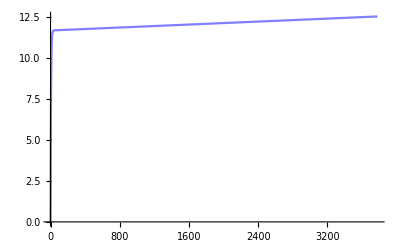

```mathematica
Ve=7707.0;
α=0.000213;
β=0.00003;
ρ=0.192886;
T=3780;
Q0=10397.0;
B0
p1=Plot[c1[t],{t,0,T},PlotRange->Automatic,PlotStyle->Directive[Opacity[0.5],Red],AxesOrigin->{0,0}];
p2=Plot[c2[t],{t,0,T},PlotRange->Automatic,PlotStyle->Directive[Opacity[0.5],Blue],AxesOrigin->{0,0}];
plot=Show[{p2,p1}]
```

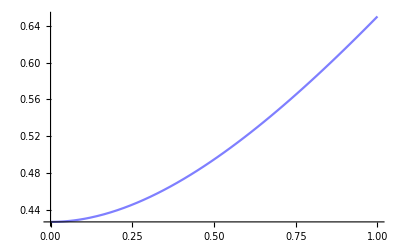

-Graphics-

```mathematica
AxesOrigin->{0,0}]
```